```mathematica
(*In this notebook I investigate the kernel in the following 2 limits: Sub horizon source with (I) sub horizon Green's, (II) super horizon Green's*)
```

## {(sub,sub)-(source,Green’s)} I_J and I_Y

```mathematica
(*Subhorizon source, subhorizon Green's*)
(*Subscript[I, J]*)
```

```mathematica
FullSimplify[Integrate[x^(-1-b)*Cos[x-((b+1)Pi)/2]*(Cos[x*s-(b+1)Pi]+(b+2)/(b+1)Cos[x*s-(b+3)Pi]+(2b+3)/(b+1)Cos[x*d]),x]]
```

1/(4 (1+b))ⅈ (3+2 b) ⅇ^(-3/2 ⅈ b π) x^-b (ⅇ^(ⅈ b π) (ExpIntegralE[1+b,ⅈ (-1+d) x]+ExpIntegralE[1+b,-ⅈ (1+d) x]+ExpIntegralE[1+b,-ⅈ (-1+s) x])-ⅇ^(2 ⅈ b π) (ExpIntegralE[1+b,-ⅈ (-1+d) x]+ExpIntegralE[1+b,ⅈ (1+d) x]+ExpIntegralE[1+b,ⅈ (-1+s) x])-ExpIntegralE[1+b,-ⅈ (1+s) x]+ⅇ^(3 ⅈ b π) ExpIntegralE[1+b,ⅈ (1+s) x])

```mathematica
SubIj[x_,c_,b_,d_,s_]:=(2/Pi)^(5/2)1/(c*4 (1+b)Sqrt[(d+s)(s-d)])ⅈ (3+2 b) ⅇ^(-3/2 ⅈ b π) x^-b (ⅇ^(ⅈ b π) (ExpIntegralE[1+b,ⅈ (-1+d) x]+ExpIntegralE[1+b,-ⅈ (1+d) x]+ExpIntegralE[1+b,-ⅈ (-1+s) x])-ⅇ^(2 ⅈ b π) (ExpIntegralE[1+b,-ⅈ (-1+d) x]+ExpIntegralE[1+b,ⅈ (1+d) x]+ExpIntegralE[1+b,ⅈ (-1+s) x])-ExpIntegralE[1+b,-ⅈ (1+s) x]+ⅇ^(3 ⅈ b π) ExpIntegralE[1+b,ⅈ (1+s) x]) ;
```

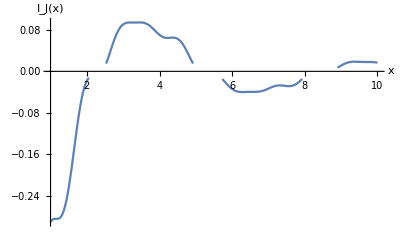

```mathematica
(*Plugging in some typical values*)
Plot[SubIj[x,0.3,0.2,0.1,6],{x,1,10},AxesLabel->{"x","I_J(x)"}]
```

```mathematica
(*clearly this ans doesn't like f(x)=0, or at least f(x)<<1. Can we use the other limit ans for this?*)
(*I think, in fact, we can use the limit that x>>1, but lets double check*)
```

```mathematica
FullSimplify[ExpToTrig[Integrate[x^(-1-b)*Sin[x-((b+1)Pi)/2]*(Cos[x*s-(b+1)Pi]+(b+2)/(b+1)Cos[x*s-(b+3)Pi]+(2b+3)/(b+1)Cos[x*d]),x]]]
```

```mathematica
SubIy[x_,c_,b_,d_,s_]:=(2/Pi)^(5/2)1/(c*4(1+b)Sqrt[(d+s)(s-d)])(3+2 b) ⅇ^(-3/2 ⅈ b π) x^-b (ⅇ^(ⅈ b π) (ExpIntegralE[1+b,ⅈ (-1+d) x]+ExpIntegralE[1+b,-ⅈ (1+d) x]-ExpIntegralE[1+b,-ⅈ (-1+s) x])+ⅇ^(2 ⅈ b π) (ExpIntegralE[1+b,-ⅈ (-1+d) x]+ExpIntegralE[1+b,ⅈ (1+d) x]-ExpIntegralE[1+b,ⅈ (-1+s) x])-ExpIntegralE[1+b,-ⅈ (1+s) x]-ⅇ^(3 ⅈ b π) ExpIntegralE[1+b,ⅈ (1+s) x]) ;
```

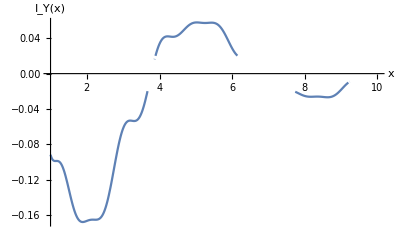

```mathematica
Plot[SubIy[x,0.3,0.2,0.1,6],{x,1,10},AxesLabel->{"x","I_Y(x)"}]
```

## {(sub,sub)-(source,Green’s)} Kernel

```mathematica
(*We have the following situation: we have the integral for the sub(Green's)-sub(source) limit, however this isn't defined for small (O(0.01)) Subscript[I, J/Y].*)
SubSubLimitI[x_,c_,b_,d_,s_]:=Pi*4^b Gamma[b+3/2]^2(2b+3)/(b+2)((x(d+s)(s-d))/4)^(-b-1/2)(BesselJ[b+1/2,x]SubIj[x,c,b,d,s]-BesselY[b+1/2,x]SubIy[x,c,b,d,s]);
```

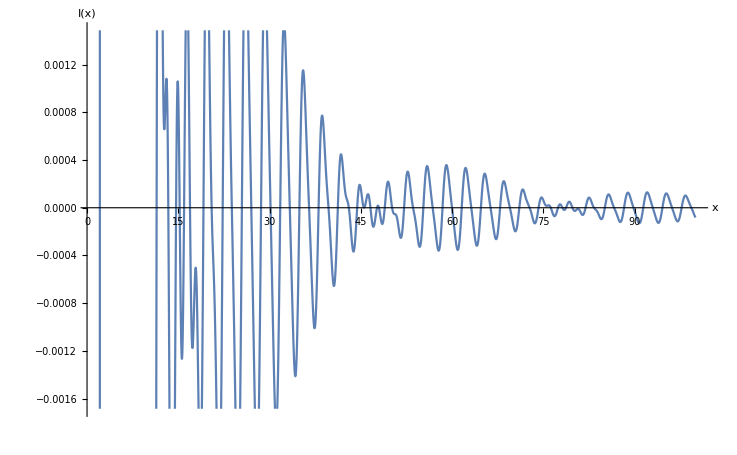

```mathematica
Plot[SubSubLimitI[x,0.3,0.2,0.1,2],{x,1,100},AxesLabel->{"x","I(x)"}]
```

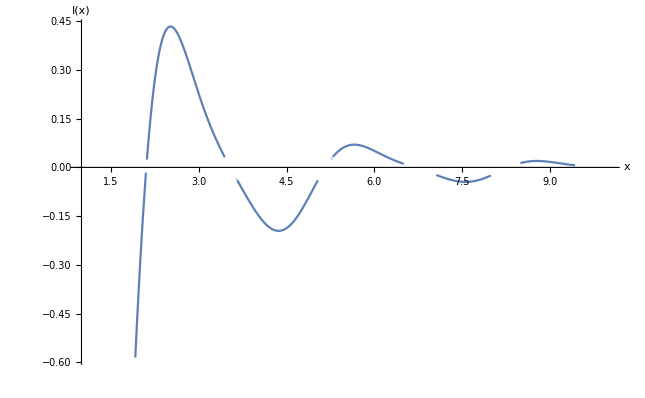

```mathematica
Plot[SubSubLimitI[x,0.3,0.2,0.1,2],{x,1,10},AxesLabel->{"x","I(x)"}]
```

## {(sub,super)-(source,Green’s)} I_J and I_Y

```mathematica
(*Subscript[I, J]*)
SuperIj[x_,c_,b_,d_,s_]:=2/(Pi*Sqrt[(d+s)(s-d)])*2^(-b-1/2)/Gamma[b+3/2]*(3+2b)/(1+b)*((Cos[x*d]+x*d*Sin[x*d]-1)/d^2+(Cos[b*Pi]-Cos[b*Pi-x*s]+x*s*Sin[b*Pi-x*s])/s^2);
```

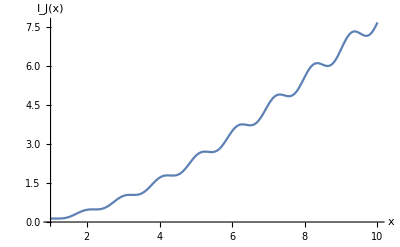

```mathematica
(*Plugging in some typical values*)
Plot[SuperIj[x,0.3,0.2,0.1,6],{x,1,10},AxesLabel->{"x","I_J(x)"}]
```

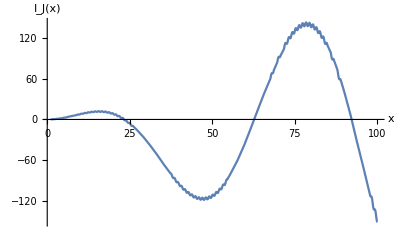

```mathematica
Plot[SuperIj[x,0.3,0.2,0.1,6],{x,1,100},AxesLabel->{"x","I_J(x)"}]
```

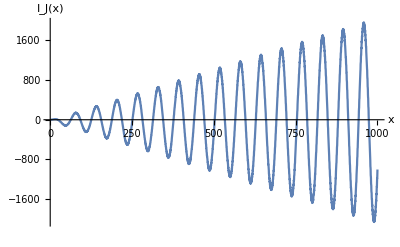

```mathematica
Plot[SuperIj[x,0.3,0.2,0.1,6],{x,1,1000},AxesLabel->{"x","I_J(x)"}]
```

```mathematica
(*Subscript[I, Y]*)
SuperIy[x_,c_,b_,d_,s_]:=-1/(Pi^2 Sqrt[(d+s)(s-d)])*2^(b+1/2)/Gamma[b+1/2]*((3+2b)x^(1-2b))/((b^2-1)(2b-1))*(-2(b-1)Hypergeometric2F1[1/2-b,1/2,3/2-b,(-d^2 x^2)/4]-Cos[b*Pi]Hypergeometric2F1[1/(2-b),1/2,3/2-b,(-s^2 x^2)/4]+(2b-1)*s*x*Sin[b*Pi]Hypergeometric2F1[1-b,3/2,2-b,(-s^2 x^2)/4])
```

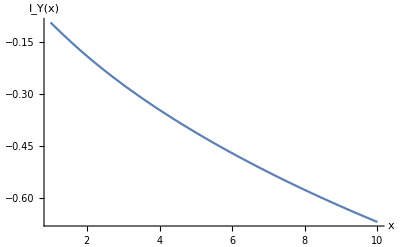

```mathematica
Plot[SuperIy[x,0.3,0.2,0.1,6],{x,1,10},AxesLabel->{"x","I_Y(x)"}]
```

## {(sub,super)-(source,Green’s)} Kernel

```mathematica
SubSuperLimitI[x_,c_,b_,d_,s_]:=Pi*4^b Gamma[b+3/2]^2(2b+3)/(b+2)((x(d+s)(s-d))/4)^(-b-1/2)(BesselJ[b+1/2,x]SuperIj[x,c,b,d,s]-BesselY[b+1/2,x]SuperIy[x,c,b,d,s]);
```

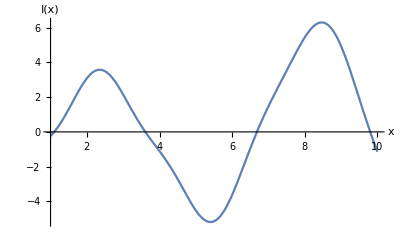

```mathematica
Plot[SubSuperLimitI[x,0.3,0.2,0.1,2],{x,1,10},AxesLabel->{"x","I(x)"}]
```

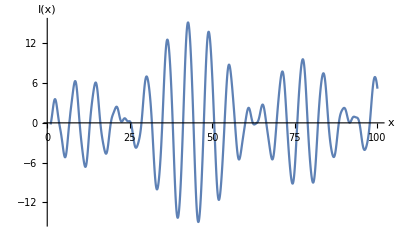

```mathematica
Plot[SubSuperLimitI[x,0.3,0.2,0.1,2],{x,1,100},AxesLabel->{"x","I(x)"}]
```

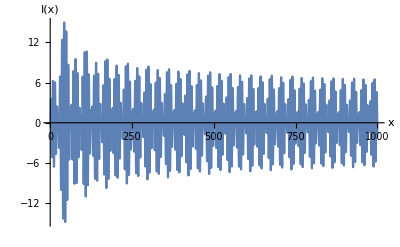

```mathematica
Plot[SubSuperLimitI[x,0.3,0.2,0.1,2],{x,1,1000},AxesLabel->{"x","I(x)"}]
```

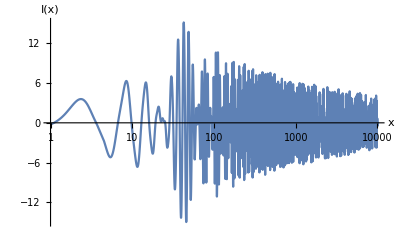

```mathematica
LogLinearPlot[SubSuperLimitI[x,0.3,0.2,0.1,2],{x,1,10000},AxesLabel->{"x","I(x)"}]
```